# Simulating BZ Life Forms using a Phenomenological Model

#### Abhishek Sharma Cronin Lab University of Glasgow

THIS FILE ANALYSES THE GENERATED DATA FROM THE SIMULATION. THE DATA SHOULD BE AT THE RIGHT PATH.

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/

## Analyze BZ data

```mathematica
nRuns=25;nSteps=10000;
```

```mathematica
analyzeAllData[nCells_,runID_]:=Module[{allPWMStates,allCAStates},
allPWMStates=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[nCells]<>".mx"];allCAStates=Import[baseDirectory<>"CA_data"<>ToString[runID]<>"_"<>ToString[nCells]<>".mx"];
Length[Position[allPWMStates⟦#⟧,3]]&/@Range[nSteps]]
```

```mathematica
popLifeForms10=analyzeAllData[10,#]&/@Range[nRuns];
```

```mathematica
popLifeForms20=analyzeAllData[20,#]&/@Range[nRuns];
```

```mathematica
popLifeForms50=analyzeAllData[50,#]&/@Range[nRuns];
```

```mathematica
popLifeForms100=analyzeAllData[100,#]&/@Range[nRuns];
```

```mathematica
popLifeForms150=analyzeAllData[150,#]&/@Range[nRuns];
```

```mathematica
Dimensions/@{popLifeForms10,popLifeForms20,popLifeForms50,popLifeForms100,popLifeForms150}
```

{{25,10000},{25,10000},{25,10000},{25,10000},{25,10000}}

```mathematica
GraphicsGrid[Partition[ListPlot[popLifeForms50⟦#⟧,Joined-> True,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/2}],None}},PlotStyle->{Black,PointSize[0.01]},ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},Frame-> True,AspectRatio->1,FrameLabel->{"Time Step","BZ Life Forms"}]&/@Range[Length[popLifeForms50]],5],Spacings->{-1,-1},ImageSize->1000]
```

```mathematica
p1=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms10],StandardDeviation[popLifeForms10]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/2}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,12},Epilog->{Inset[Style["Cells Size = 10x10",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms10],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p2=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms20],StandardDeviation[popLifeForms20]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/2}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,23},Epilog->{Inset[Style["Cells Size = 20x20",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms20],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p3=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms50],StandardDeviation[popLifeForms50]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/2}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,50},Epilog->{Inset[Style["Cells Size = 50x50",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms50],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p4=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms100],StandardDeviation[popLifeForms100]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/2}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,170},Epilog->{Inset[Style["Cells Size = 100x100",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms100],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p5=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms150],StandardDeviation[popLifeForms150]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/2}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,350},Epilog->{Inset[Style["Cells Size = 150x150",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms150],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
plot1=GraphicsColumn[{GraphicsRow[{p1,p2,p3},Spacings->{-10,-10}],GraphicsRow[{p4,p5},Spacings->{-10,-10}]},Spacings->-10,ImageSize->600]
```

```mathematica
Export[baseDirectory<>"plot1.png",plot1,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1.png

```mathematica
Export[baseDirectory<>"plot1.svg",plot1]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1.svg

```mathematica
Length[Mean[popLifeForms10]]
```

10000

```mathematica
{Mean[Mean[popLifeForms10]⟦9900;;10000⟧//N],Mean[Mean[popLifeForms20]⟦9900;;10000⟧//N],Mean[Mean[popLifeForms50]⟦9900;;10000⟧//N],Mean[Mean[popLifeForms100]⟦9900;;10000⟧//N],Mean[Mean[popLifeForms150]⟦9900;;10000⟧//N]}
```

{1.28119,4.45149,28.6721,121.422,271.21}

```mathematica
avgSpecies10=1;
avgSpecies20=4;
avgSpecies50=35;
avgSpecies100=120;
avgSpecies150=270;
```

```mathematica
ListLogPlot[{Mean[popLifeForms10],Mean[popLifeForms20],Mean[popLifeForms50],Mean[popLifeForms100],Mean[popLifeForms150]},PlotStyle-> {{Red,PointSize[0.015]},{Orange,PointSize[0.015]},{Darker[Green],PointSize[0.015]},{Darker[Magenta],PointSize[0.015]},{Darker[Blue],PointSize[0.015]}},PlotRange-> Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps/2}],None}},FrameLabel->{"Time Step","BZ Life Forms"},PlotLegends-> Placed[LineLegend[{"10","20","50","100","150"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Cell Size",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.16,0.8}],ImageSize->300]
```

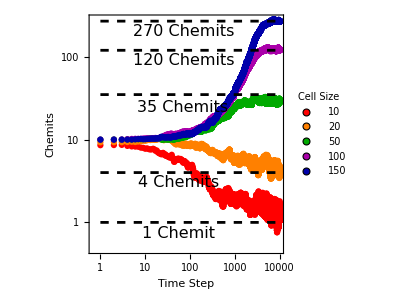

```mathematica
plot2=Show[{ListLogLogPlot[{Mean[popLifeForms10],Mean[popLifeForms20],Mean[popLifeForms50],Mean[popLifeForms100],Mean[popLifeForms150]},PlotStyle-> {{Red,PointSize[0.015]},{Orange,PointSize[0.015]},{Darker[Green],PointSize[0.015]},{Darker[Magenta],PointSize[0.015]},{Darker[Blue],PointSize[0.015]}},PlotRange-> Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},Frame->True,AspectRatio->1,FrameLabel->{"Time Step","Chemits"},PlotLegends-> Placed[LineLegend[{"10","20","50","100","150"},LegendMarkers->Graphics[Disk[]],Background-> White,LegendLabel-> "Cell Size",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.15,0.75}],ImageSize->300],LogLogPlot[#,{i,1,10000},PlotStyle-> {Black,Dashing-> 0.02}]&/@{avgSpecies10,avgSpecies20,avgSpecies50,avgSpecies100,avgSpecies150},Graphics[{Text[Style["1 Chemit",16,Italic],{4,-0.3}],Text[Style["4 Chemits",16,Italic],{4,1.1}],Text[Style["35 Chemits",16,Italic],{4.2,3.2}],Text[Style["120 Chemits",16,Italic],{4.3,4.5}],Text[Style["270 Chemits",16,Italic],{4.3,5.3}]}]}]
```

```mathematica
Export[baseDirectory<>"plot2.png",plot2,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot2.png

```mathematica
Export[baseDirectory<>"plot2.svg",plot2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot2.svg

```mathematica
Export[baseDirectory<>"plot2.png",plot2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot2.png

## BZ Correlations

In this section, we estimate the spatial correlations between the living species and estimate the birth and death rates vs. time. The criteria to detect the emergence of new state from self-replication or propagation step consists of the following :

(1) Getting the list of cell states with PWM levels 3 at time step t and t+1
(2) Finding the still states which stays the same at t and t+1
(3) Getting list of new states formed at t+1 (states which were not present at t)
(4) If there is an appearance of new state and and nearest neighbour disappeared : Propagation
(5) If there is a next nearest neighbour present and no change in nearest neighbours : Replication

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/

```mathematica
nRuns=25;nSteps=10000;runID=25;nCells=100;
```

```mathematica
boundC[x_,y_]:={ Which[x==0,nCells,x==nCells+1,1,x>0&&x<nCells+1,x],Which[y== 0,nCells,y==nCells+1,1,y>0&&y<nCells+1,y]}
```

```mathematica
opTypes[PWMStates_,timeStep_]:=Block[{oldStates,newStates,stillStates,diff,oS, nS,nnList,nnnList,newStates1,newStates2,prop,rep,annh,comb1,comb2},
oldStates=Position[PWMStates⟦timeStep⟧,3]; 
newStates=Position[PWMStates⟦timeStep+1⟧,3];
diff=(Length@newStates-Length@oldStates);
stillStates=Intersection[oldStates,newStates];
oS=Delete[oldStates,Flatten[Position[oldStates,#]&/@stillStates,1]];(* Old States Disappered : Propagation and Annihiliation *)
nS=Delete[newStates,Flatten[Position[newStates,#]&/@stillStates,1]];
(* New States Appeared : Propagation and Replication *)
nnList={{#⟦1⟧-1,#⟦2⟧},{#⟦1⟧,#⟦2⟧-1},{#⟦1⟧+1,#⟦2⟧},{#⟦1⟧,#⟦2⟧+1}}&/@nS; 
nnnList={{#⟦1⟧-1,#⟦2⟧-1},{#⟦1⟧-1,#⟦2⟧+1},{#⟦1⟧+1,#⟦2⟧-1},{#⟦1⟧+1,#⟦2⟧+1}}&/@nS; 
nnList=Apply[boundC,nnList,{2}];
nnnList=Apply[boundC,nnnList,{2}];
newStates1=Table[{i,Length@Flatten[Position[oS,#]&/@nnList⟦i⟧]},{i,Length[nS]}];
newStates2=Table[{i,Length@Flatten[Position[oldStates,#]&/@nnnList⟦i⟧]},{i,Length[nS]}];
comb1=Length[Select[Table[If[newStates1⟦i,2⟧==0 && newStates2⟦i,2⟧== 0,1,0],{i,Length[nS]}],#==1&]];
comb2=Length[Select[Table[If[newStates1⟦i,2⟧>0 && newStates2⟦i,2⟧>0,1,0],{i,Length[nS]}],#==1&]];
prop=Length[Select[Table[If[newStates1⟦i,2⟧>0 && newStates2⟦i,2⟧== 0,1,0],{i,Length[nS]}],#== 1&]]+(comb1+comb2);
rep=Length[Select[Table[If[newStates1⟦i,2⟧==0 && newStates2⟦i,2⟧>0,1,0],{i,Length[nS]}],#==1&]]+(comb1+comb2);
annh=diff-rep;
{Length@nS,prop,rep,annh,comb1,comb2}
]
```

```mathematica
AnalyzeCells[cellSize_,runID_]:=Module[{PWMStates,outData},
PWMStates=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[cellSize]<>".mx"];
outData=Table[opTypes[PWMStates,timeStep],{timeStep,Length[PWMStates]-1}];
Return[outData]]
```

```mathematica
data1=Monitor[ParallelTable[AnalyzeCells[10,i],{i,nRuns}],i];
```

```mathematica
data2=Monitor[ParallelTable[AnalyzeCells[20,i],{i,nRuns}],i];
```

```mathematica
data3=Monitor[ParallelTable[AnalyzeCells[50,i],{i,nRuns}],i];
```

```mathematica
data4=Monitor[ParallelTable[AnalyzeCells[100,i],{i,nRuns}],i];
```

```mathematica
data5=Monitor[ParallelTable[AnalyzeCells[150,i],{i,nRuns}],i];
```

```mathematica
Dimensions/@{data1,data2,data3,data4,data5}
```

{{25,10000,6},{25,10000,6},{25,10000,6},{25,10000,6},{25,10000,6}}

```mathematica
p1a=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data1⟦All,All,2⟧],StandardDeviation[data1⟦All,All,2⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Propagation Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,4}],ListPlot[Mean[data1⟦All,All,2⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p1b=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data1⟦All,All,3⟧],StandardDeviation[data1⟦All,All,3⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,1.5}],ListPlot[Mean[data1⟦All,All,3⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p1c=Block[{dat=Table[Accumulate[data1⟦All,All,3⟧⟦i⟧],{i,Length@data1}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum.  Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,1200}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p1d=Block[{dat=Table[Accumulate[data1⟦All,All,4⟧⟦i⟧],{i,Length@data1}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-2500}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p1=GraphicsGrid[Partition[{p1a,p1b,p1c,p1d},2],Spacings->{-10,-10},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"plot1a.png",p1,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1a.png

```mathematica
Export[baseDirectory<>"plot1a.svg",p1]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1a.svg

```mathematica
p2a=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data2⟦All,All,2⟧],StandardDeviation[data2⟦All,All,2⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Propagation Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,6}],ListPlot[Mean[data2⟦All,All,2⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p2b=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data2⟦All,All,3⟧],StandardDeviation[data2⟦All,All,3⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,2}],ListPlot[Mean[data2⟦All,All,3⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p2c=Block[{dat=Table[Accumulate[data2⟦All,All,3⟧⟦i⟧],{i,Length@data2}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum.  Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,2500}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p2d=Block[{dat=Table[Accumulate[data2⟦All,All,4⟧⟦i⟧],{i,Length@data2}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-2500}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p2=GraphicsGrid[Partition[{p2a,p2b,p2c,p2d},2],Spacings->{0,0},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"plot1b.png",p2,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1b.png

```mathematica
Export[baseDirectory<>"plot1b.svg",p2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1b.svg

```mathematica
p3a=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data3⟦All,All,2⟧],StandardDeviation[data3⟦All,All,2⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Propagation Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,15}],ListPlot[Mean[data3⟦All,All,2⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p3b=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data3⟦All,All,3⟧],StandardDeviation[data3⟦All,All,3⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,3}],ListPlot[Mean[data3⟦All,All,3⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p3c=Block[{dat=Table[Accumulate[data3⟦All,All,3⟧⟦i⟧],{i,Length@data3}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum.  Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,10000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p3d=Block[{dat=Table[Accumulate[data3⟦All,All,4⟧⟦i⟧],{i,Length@data3}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-10000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p3=GraphicsGrid[Partition[{p3a,p3b,p3c,p3d},2],Spacings->{-10,-10},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"plot1c.png",p3,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1c.png

```mathematica
Export[baseDirectory<>"plot1c.svg",p3]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1c.svg

```mathematica
p4a=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data4⟦All,All,2⟧],StandardDeviation[data4⟦All,All,2⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Propagation Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,50}],ListPlot[Mean[data4⟦All,All,2⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p4b=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data4⟦All,All,3⟧],StandardDeviation[data4⟦All,All,3⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,6}],ListPlot[Mean[data4⟦All,All,3⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p4c=Block[{dat=Table[Accumulate[data4⟦All,All,3⟧⟦i⟧],{i,Length@data4}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum.  Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p4d=Block[{dat=Table[Accumulate[data4⟦All,All,4⟧⟦i⟧],{i,Length@data4}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p4=GraphicsGrid[Partition[{p4a,p4b,p4c,p4d},2],Spacings->{-10,-10},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"plot1d.png",p4,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1d.png

```mathematica
Export[baseDirectory<>"plot1d.svg",p4]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1d.svg

```mathematica
p5a=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data5⟦All,All,2⟧],StandardDeviation[data5⟦All,All,2⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Propagation Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,100}],ListPlot[Mean[data5⟦All,All,2⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p5b=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[data5⟦All,All,3⟧],StandardDeviation[data5⟦All,All,3⟧]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Avg. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,65}],ListPlot[Mean[data5⟦All,All,3⟧],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300];
```

```mathematica
p5c=Block[{dat=Table[Accumulate[data5⟦All,All,3⟧⟦i⟧],{i,Length@data5}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum.  Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,100000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p5d=Block[{dat=Table[Accumulate[data5⟦All,All,4⟧⟦i⟧],{i,Length@data5}]},
Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat],StandardDeviation[dat]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-100000}],ListPlot[Mean[dat],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 300]];
```

```mathematica
p5=GraphicsGrid[Partition[{p5a,p5b,p5c,p5d},2],Spacings->{-10,-10},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"plot1e.png",p5,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1e.png

```mathematica
Export[baseDirectory<>"plot1e.svg",p5]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1e.svg

```mathematica
plot1=Block[{
dat1=Table[Accumulate[data1⟦All,All,3⟧⟦i⟧],{i,Length@data1}],
dat2=Table[Accumulate[data2⟦All,All,3⟧⟦i⟧],{i,Length@data2}],
dat3=Table[Accumulate[data3⟦All,All,3⟧⟦i⟧],{i,Length@data3}],
dat4=Table[Accumulate[data4⟦All,All,3⟧⟦i⟧],{i,Length@data4}],
dat5=Table[Accumulate[data5⟦All,All,3⟧⟦i⟧],{i,Length@data5}]},

Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat1],StandardDeviation[dat1]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Red,Opacity[ 0.01]},FrameLabel->{"Time Step"," Cum. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat2],StandardDeviation[dat2]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Orange,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat3],StandardDeviation[dat3]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Green],Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat4],StandardDeviation[dat4]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Blue],Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat5],StandardDeviation[dat5]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Brown,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Replication Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,20000}],

ListPlot[{Mean[dat1],Mean[dat2],Mean[dat3],Mean[dat4],Mean[dat5]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{{Red,PointSize[0.01]},{Orange,PointSize[0.01]},{Darker[Green],PointSize[0.01]},{Darker[Blue],PointSize[0.01]},{Brown,PointSize[0.01]}},PlotLegends-> Placed[LineLegend[{"10","20","50","100","150"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Cell Size",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.35,0.75}],PlotMarkers->None,Frame-> True]},ImageSize-> 300]]
```

```mathematica
Export[baseDirectory<>"plot_Rep.png",plot1,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot_Rep.png

```mathematica
Export[baseDirectory<>"plot_Rep.svg",plot1]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot_Rep.svg

```mathematica
plot2=Block[{
dat1=Table[Accumulate[data1⟦All,All,4⟧⟦i⟧],{i,Length@data1}],
dat2=Table[Accumulate[data2⟦All,All,4⟧⟦i⟧],{i,Length@data2}],
dat3=Table[Accumulate[data3⟦All,All,4⟧⟦i⟧],{i,Length@data3}],
dat4=Table[Accumulate[data4⟦All,All,4⟧⟦i⟧],{i,Length@data4}],
dat5=Table[Accumulate[data5⟦All,All,4⟧⟦i⟧],{i,Length@data5}]},

Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat1],StandardDeviation[dat1]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Red,Opacity[ 0.01]},FrameLabel->{"Time Step"," Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat2],StandardDeviation[dat2]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Orange,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat3],StandardDeviation[dat3]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Green],Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat4],StandardDeviation[dat4]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Blue],Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat5],StandardDeviation[dat5]}],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Brown,Opacity[ 0.01]},FrameLabel->{"Time Step","Cum. Death Events"},PlotMarkers->None,Frame-> True,PlotRange-> {0,-20000}],

ListPlot[{Mean[dat1],Mean[dat2],Mean[dat3],Mean[dat4],Mean[dat5]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{{Red,PointSize[0.01]},{Orange,PointSize[0.01]},{Darker[Green],PointSize[0.01]},{Darker[Blue],PointSize[0.01]},{Brown,PointSize[0.01]}},PlotLegends-> Placed[LineLegend[{"10","20","50","100","150"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Cell Size",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.35,0.25}],PlotMarkers->None,Frame-> True]},ImageSize-> 300]]
```

```mathematica
Export[baseDirectory<>"plot_Death.png",plot2,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot_Death.png

```mathematica
Export[baseDirectory<>"plot_Death.svg",plot2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot_Death.svg

```mathematica
plot3=Block[{
dat1=Table[Accumulate[data1⟦All,All,3⟧⟦i⟧]+Accumulate[data1⟦All,All,4⟧⟦i⟧],{i,Length@data1}],
dat2=Table[Accumulate[data2⟦All,All,3⟧⟦i⟧]+Accumulate[data2⟦All,All,4⟧⟦i⟧],{i,Length@data2}],
dat3=Table[Accumulate[data3⟦All,All,3⟧⟦i⟧]+Accumulate[data3⟦All,All,4⟧⟦i⟧],{i,Length@data3}],
dat4=Table[Accumulate[data4⟦All,All,3⟧⟦i⟧]+Accumulate[data4⟦All,All,4⟧⟦i⟧],{i,Length@data4}],dat5=Table[Accumulate[data5⟦All,All,3⟧⟦i⟧]+Accumulate[data5⟦All,All,4⟧⟦i⟧],{i,Length@data5}]},

Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat1],StandardDeviation[dat1]}],Axes-> False,AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Red,Opacity[ 0.01]},FrameLabel->{"Time Step","Net Cumulative Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-10,130}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat2],StandardDeviation[dat2]}],Axes-> False,AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Orange,Opacity[ 0.01]},FrameLabel->{"Time Step","Net Cumulative Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-10,130}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat3],StandardDeviation[dat3]}],Axes-> False,AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Green],Opacity[ 0.01]},FrameLabel->{"Time Step","Net Cumulative Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-10,130}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat4],StandardDeviation[dat4]}],Axes-> False,AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Blue],Opacity[ 0.01]},FrameLabel->{"Time Step","Net Cumulative Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-10,130}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat5],StandardDeviation[dat5]}],Axes-> False,AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Brown,Opacity[ 0.01]},FrameLabel->{"Time Step","Net Cumulative Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-10,130}],

ListPlot[{Mean[dat1],Mean[dat2],Mean[dat3],Mean[dat4],Mean[dat5]},Axes-> False,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{{Red,PointSize[0.01]},{Orange,PointSize[0.01]},{Darker[Green],PointSize[0.01]},{Darker[Blue],PointSize[0.01]},{Darker[Brown],PointSize[0.01]}},PlotLegends-> Placed[LineLegend[{"10","20","50","100","150"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Life Forms",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.8,0.2}],PlotMarkers->None,Frame-> True]},ImageSize-> 300]]
```

```mathematica
plot4=Block[{
dat1=Table[Accumulate[data1⟦All,All,3⟧⟦i⟧]+Accumulate[data1⟦All,All,4⟧⟦i⟧],{i,Length@data1}],
dat2=Table[Accumulate[data2⟦All,All,3⟧⟦i⟧]+Accumulate[data2⟦All,All,4⟧⟦i⟧],{i,Length@data2}],
dat3=Table[Accumulate[data3⟦All,All,3⟧⟦i⟧]+Accumulate[data3⟦All,All,4⟧⟦i⟧],{i,Length@data3}],
dat4=Table[Accumulate[data4⟦All,All,3⟧⟦i⟧]+Accumulate[data4⟦All,All,4⟧⟦i⟧],{i,Length@data4}],dat5=Table[Accumulate[data5⟦All,All,3⟧⟦i⟧]+Accumulate[data5⟦All,All,4⟧⟦i⟧],{i,Length@data5}]},

Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[dat1],StandardDeviation[dat1]}],AspectRatio->1,FrameTicks->{{{0,150,300},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Red,Opacity[ 0.01]},FrameLabel->{"Time Step","Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-15,300}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat2],StandardDeviation[dat2]}],AspectRatio->1,FrameTicks->{{{0,-400,-800},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Orange,Opacity[ 0.01]},FrameLabel->{"Time Step","Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-15,300}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat3],StandardDeviation[dat3]}],AspectRatio->1,FrameTicks->{{{0,150,300},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Green],Opacity[ 0.01]},FrameLabel->{"Time Step","Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-15,300}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat4],StandardDeviation[dat4]}],AspectRatio->1,FrameTicks->{{{0,150,300},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Darker[Blue],Opacity[ 0.01]},FrameLabel->{"Time Step","Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-15,300}],

ListPlot[MapThread[Around[#1,#2]&,{Mean[dat5],StandardDeviation[dat5]}],AspectRatio->1,FrameTicks->{{{0,150,300},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Brown,Opacity[ 0.01]},FrameLabel->{"Time Step","Events"},PlotMarkers->None,Frame-> True,PlotRange-> {-15,300}],

ListPlot[{Mean[dat1],Mean[dat2],Mean[dat3],Mean[dat4],Mean[dat5]},Axes-> False,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{{Red,PointSize[0.01]},{Orange,PointSize[0.01]},{Darker[Green],PointSize[0.01]},{Darker[Blue],PointSize[0.01]},{Brown,PointSize[0.01]}},ImageSize-> 50]}]]
```

```mathematica
Export[baseDirectory<>"cum_events1.png",plot3,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/cum_events1.png

```mathematica
Export[baseDirectory<>"cum_events1.svg",plot3]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/cum_events1.svg

```mathematica
Export[baseDirectory<>"cum_events2.png",plot4,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/cum_events2.png

```mathematica
Export[baseDirectory<>"cum_events2.svg",plot4]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/cum_events2.svg

```mathematica
plot6=ListPlot[{Mean[data1⟦All,All,2⟧],Mean[data2⟦All,All,2⟧],Mean[data3⟦All,All,2⟧],Mean[data4⟦All,All,2⟧],Mean[data5⟦All,All,2⟧]},AspectRatio->1,FrameTicks->{{Automatic,None},{Table[{i,NumberForm[ScientificForm@i,2]},{i,0.,nSteps,nSteps/3}],None}},PlotLegends-> Placed[LineLegend[{"10","20","50","100","150"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Cell Size",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.13,0.8}],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotRange-> {0,45},FrameLabel->{"Time Step","Propagation Events"},PlotStyle->{{Red,PointSize[0.01],Opacity[0.5]},{Orange,PointSize[0.01],Opacity[0.5]},{Darker[Green],PointSize[0.01],Opacity[0.5]},{Darker[Blue],PointSize[0.01],Opacity[0.5]},{Brown,PointSize[0.01],Opacity[0.5]}},PlotMarkers->None,Frame-> True,ImageSize->300]
```

```mathematica
plot7=ListLogPlot[{Mean[data1⟦All,All,2⟧],Mean[data2⟦All,All,2⟧],Mean[data3⟦All,All,2⟧],Mean[data4⟦All,All,2⟧],Mean[data5⟦All,All,2⟧]},AspectRatio->1,FrameTicks->{{{0,0.1,100},None},{Table[{i,ScientificForm@i},{i,0.,nSteps,nSteps}],None}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotRange-> Full,FrameLabel->{None,"Events"},PlotStyle->{{Red,PointSize[0.01]},{Orange,PointSize[0.01]},{Darker[Green],PointSize[0.01]},{Darker[Blue],PointSize[0.01]},{Brown,PointSize[0.01]}},PlotMarkers->None,Frame-> True,ImageSize->150]
```

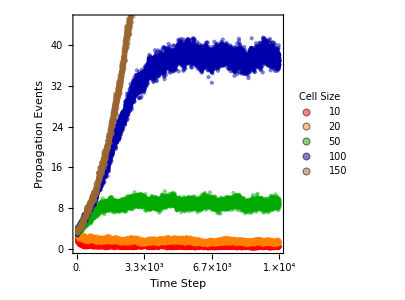
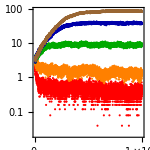

```mathematica
plot8=Show[{plot6,Graphics[Inset[plot7,{7000,21}]]}]
```

```mathematica
Export[baseDirectory<>"propg_events.png",plot8,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/propg_events.png

```mathematica
Export[baseDirectory<>"propg_events.svg",plot8]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/propg_events.svg